# Automates cellulaires

## Quentin Matinier (quentin.matinier@ens2m.org) Elie Pitiot (elie.pitiot@ens2m.org) Valentin Ruche (valentin.ruche@ens2m.org)

Résumé : ce projet aborde le sujet des automates cellulaires en commençant par refaire le célèbre Jeu de la vie jusqu’à leur utilisation pour modéliser des phénomènes réels complexes comme des propagations d’épidémies ou de feux de forêts où une multitude de paramètres interviennent. 
Mots clés : automates cellulaires, Jeu de la vie, propagation de phénomène.
Abstract : This project tackles the subject of cellular automata, starting with a remake of the famous Game of Life, right through to their use to model complex real-life phenomena such as the spread of epidemics or forest fires, where a multitude of parameters are involved.
Keywords : automatom cellular, Game of life, propagation of phenomena.

## Introduction

Les automates cellulaires sont des modèles mathématiques utilisés pour simuler des systèmes dynamiques discrets composés de cellules disposées en grille, dont l’évolution discrète (c’est-à-dire qui n’est pas continue mais se fait par pas de temps) est déterminée par des règles d’évolutions. Chaque cellules peut adopter un état souvent défini par un entier ou un réel, et son évolution dépend de l’état de ses cellules voisines. Malgré leur simplicité, ces modèles permettent de générer des comportements diversifiés et complexes. Ce domaine des mathématiques est plutôt récent car il date du milieu du XXème siècle mais a connu un véritable essor avec l’arrivée de l’informatique. Il est utile dans certains domaine comme la croissance de cristaux ou les phénomènes de propagation. Certains automates comme la fourmi de Langton [3] et le Jeu de la Vie de John Conway [2] ont grandement contribué à la popularité des automates cellulaires au-delà même du domaine scientifique.
Dans ce projet, nous commencerons par une étude des automates cellulaires classiques avec les automates 1D et 2D en nous concentrant notamment sur le Jeu de la Vie de John Conway. Ce jeu illustre comment des règles simples peuvent produire une grande variété de motifs et de comportements, fournissant une base solide pour comprendre les principes fondamentaux des automates cellulaires.
Nous élargirons ensuite notre analyse à des applications spécifiques et actuelles des automates cellulaires, telles que la modélisation de la propagation des épidémies et des feux de forêt. Nous chercherons à faire des automates cellulaires plus avancé pour simuler au mieux ces phénomènes naturels complexes.

## I. Recréer le jeu de la vie de Conway

Pour calculer l’évolution d’un automate il faut déterminer pour chaque case l’état qu’elle va prendre à l’étape suivante. Pour cela on va découper le tableaux en une liste de sous tableaux de taille précise qui seront chacun lié à une cellule du tableau, la taille de ces sous tableau correspond au cellules qui vont influencer la cellule du milieu. Par exemple nous pouvons découper le tableau en sous tableau de taille 3x3 ainsi les 8 cellules autour de la cellules centrale auront de l’influence, c’est le cas dans la plupart des automates cellulaires mais il est tout a fait possible d’adapter la taille. Pour cela on utilise la fonction Partition[tab,{n1,n2},{d1,d2}], {n1,n2} est la taille du sous tableau voulu et {d1,d2} sont les décalages entre les sous tableaux; ici ce sera simplement 1.

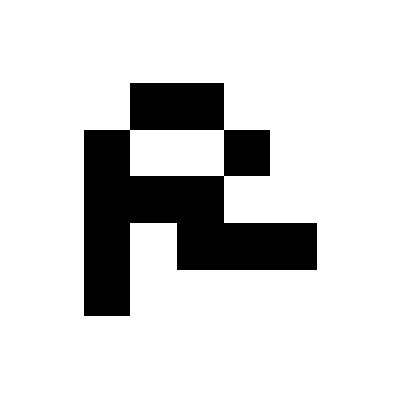

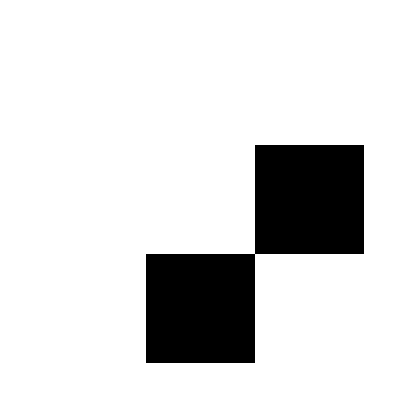
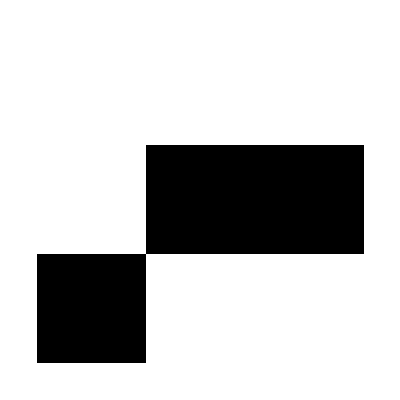
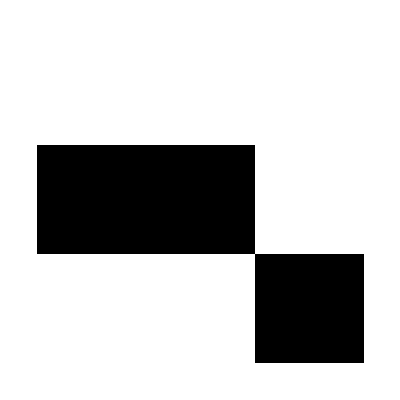
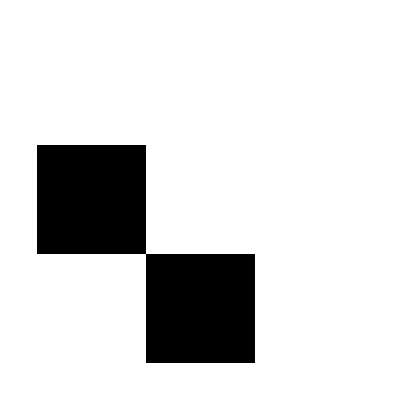
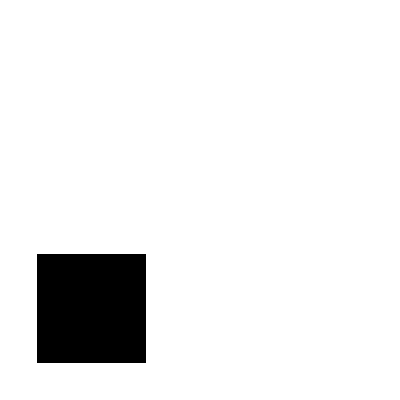
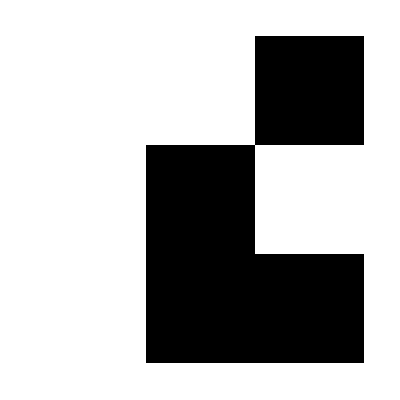
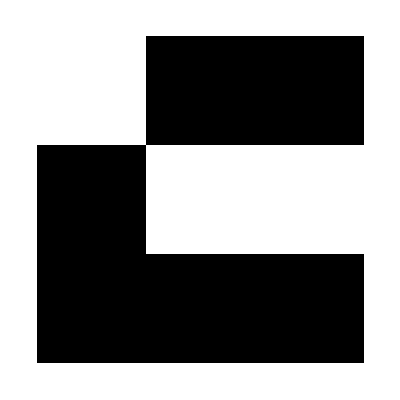

```mathematica
testbinaire = ArrayPad[RandomInteger[1,{5,5}],1,0]; (*on créé un tableau initial*)
ArrayPlot[testbinaire,ImageSize->Tiny]
(*découpe du tableau en sous tableau et affichage*)
repart = Partition[testbinaire,{3,3},{1,1}];
ArrayPlot[#, ImageSize->Tiny] & /@ Flatten[repart,1]
```

On va maintenant développer la fonction permettant de faire évoluer le tableau. Les règles du jeu de la vie sont : si une cellule blanche a 3 voisines noires elle passe en noir et si une cellule noire à 2 ou 3 voisines elle reste noire, dans les autres cas les cases deviennent blanche. Les bords du tableau sont remplis par des 0 comme si le reste du tableau était vide, pour cela on utilise la fonction Arraypad qui vient ajouter un 0 au début et à la fin de chaque liste et sous liste. Pour parcourir l’ensemble du tableaux la fonction Do[-,-]. Ici les conditions de boucle sont : {j, Length[nouveau[[1]]]}, {i, Length[nouveau]}, à chaque boucle on incrémente j de 1 jusqu’à avoir parcouru l’entièreté d’une sous liste (ce qui correspond à avoir parcouru une ligne) puis on incrémente i de 1 et recommencer l’incrémentation de j depuis 1... Comme i et j sont des variables on peut les utiliser pour parcourir le tableau, il suffit juste de traduire de manière logique les règles du Jeu de la vie. Les conditions sont légèrement différentes car dans ce code on utilise Total pour compter le nombre de cellules voisines vivantes or si la cellule que l’on veut faire évoluer est noir elle va elle aussi être compté (on aurait pu aussi écrire 2<=Total[Flatten[listevoisins[[i,j]]]] -1<= 3.)  Par ailleurs dans Total il est nécessaire d’utiliser Flatten car dans la liste des voisins est un tableau de taille 3x3 et Total ne fonctionne que sur une liste simple de profondeur 1.

```mathematica
nextGen[tab_] := Module[{nouveau,listevoisins},
  nouveau=tab;
  listevoisins = Partition[ArrayPad[tab,1], {3, 3}, {1, 1}];
  Do[
    If[(tab[[i,j]]== 1 && 3<=Total[Flatten[listevoisins[[i,j]]]] <= 4) ||
    (tab[[i,j]] == 0 && Total[Flatten[listevoisins[[i,j]]]] == 3),
     nouveau[[i,j]]=1, nouveau[[i,j]]=0
     ],
    {j, Length[nouveau[[1]]]}, {i, Length[nouveau]}];
    nouveau
]

JeuDeLaVie[init_,n_]:=NestList[nextGen,init,n];
Visualisation[listeGeneration_]:=ArrayPlot[#,Mesh->False,Frame->False,ImageSize->Tiny]&/@listeGeneration;
```

On peut vérifier que le code fonctionne en vérifiant certaines structures communes tel des structures stables, oscillantes et glider. Pour plus de détail sur les différentes classes de structures du Jeu de la vie voir [2].

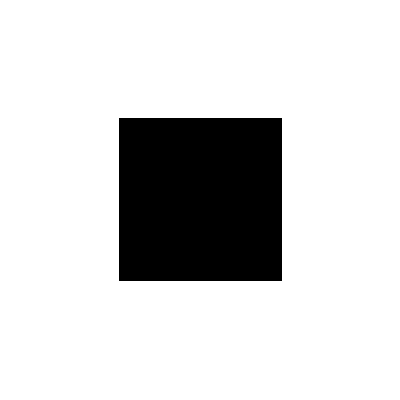
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

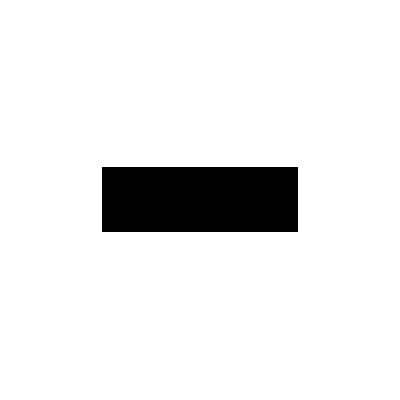
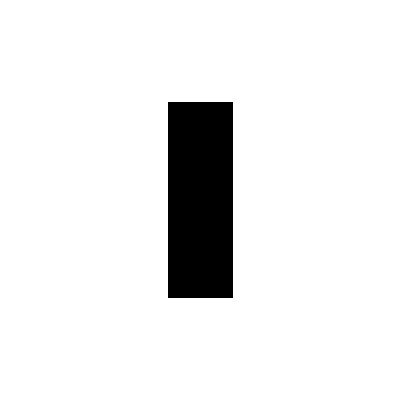
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

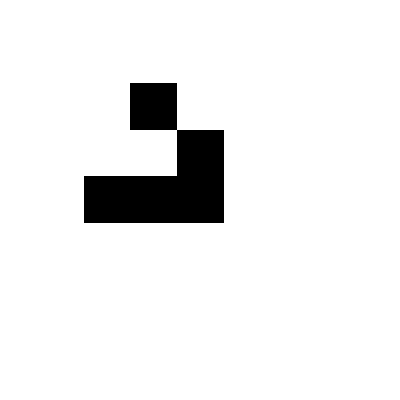
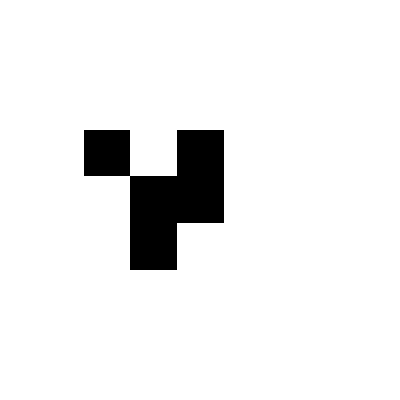
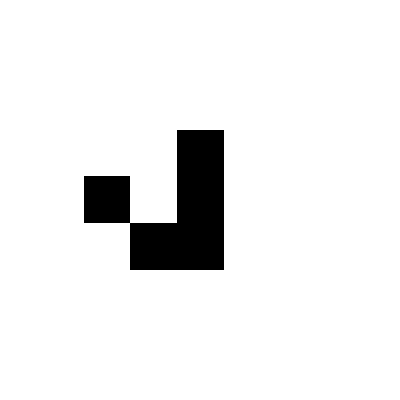
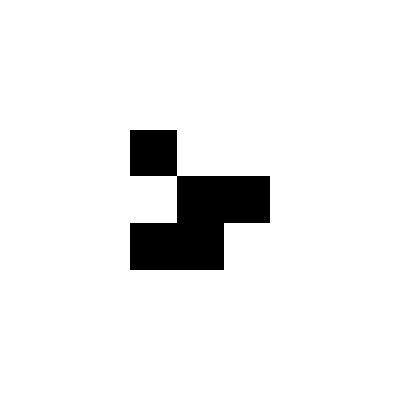
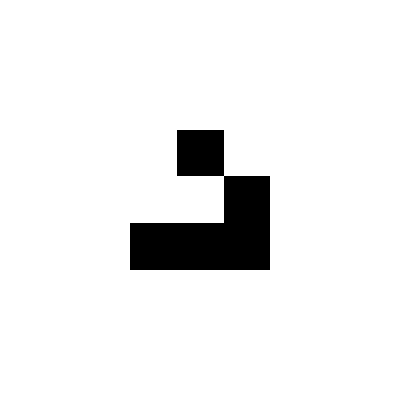
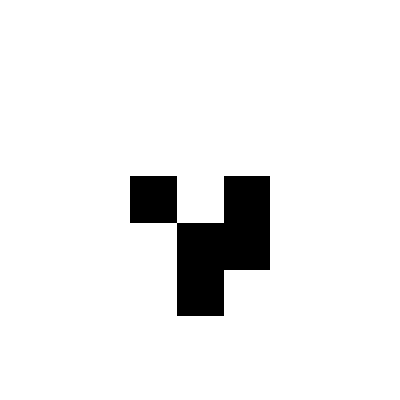

```mathematica
stable = {{0,0,0,0},{0,1,1,0},{0,1,1,0},{0,0,0,0}};
blinker = {{0,0,0,0,0},{0,0,0,0,0},{0,1,1,1,0},{0,0,0,0,0},{0,0,0,0,0}};
glider = {{0,0,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,1,0,0,0},{0,1,1,1,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}};

Visualisation[JeuDeLaVie[stable,5]]
Visualisation[JeuDeLaVie[blinker,5]]
Visualisation[JeuDeLaVie[glider,5]]
```

On observe bien les même résultat que ceux du Jeu de la vie de Conway, on peut faire une simulation d’une grille plus grande

```mathematica
init1=ArrayPad[RandomInteger[1,{20,20}], 1, 0];
evolution = JeuDeLaVie[init1,20];

(*ListAnimate[ArrayPlot[#, Mesh -> True, Frame -> False, ImageSize -> 300] & /@ evolution]*)
ArrayPlot[#, Mesh -> False, Frame -> False, ImageSize->Tiny] & /@ evolution
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Maintenant que nous avons achevé le Jeu de la vie nous pouvons reprendre une même structure de programme mais en y ajoutant plus de conditions et d’états de cellules possible pour faire des simulations de phénomènes plus complexes.

## II. Application à la propagation d’épidémie

On va maintenant s’intéresser à différents types de propagation à commencer par la propagation d’épidémie. Plusieurs hypothèses et simplification sont à prendre en compte, en effet nous sommes dans un environnement statique dans le sens où il n’y a pas de déplacement de personnes. Il faut donc voir la grille non pas comme une zone spatiale où chaque individu est en contact physique avec ceux autour mais plutôt comme une “carte” recensant tout les individus et leur contact social, chaque individu ayant donc 8 voisins. Cette première hypothèse assez grossière, peu réaliste, pourra être amenée à changer au cours de l’affinement du modèle en diminuant notamment la densité d’individus. Par ailleurs nous ne prendrons pas en compte des effets de mise en quarantaine et de confinement ou de campagne vaccinale. En effet pour le cas du vaccin toutes les cellules vaccinées le seront dès le début et aucune cellule ne se fera vacciner au cours de l’épidémie. Pour finir nous considérons une population hétérogène dans le sens où tous les individus ont la même probabilité de tomber malades ou de mourir et mettent tous autant de temps à guérir. Pour la gestion des effets de bords nous considérerons que le tableau à une forme de tore, c’est à dire que le bord haut du tableau est connecté au bord bas, de même pour les bord gauche et droite. 
Il faut donc définir les différent types d’état de cellule et leurs règles d’évolution. Nous allons définir chaque état par un entier pour pouvoir être interprété par le code et une couleur pour pouvoir afficher, on aura:
	- Des cellules saines = 0 : à chaque itération on regarde les cellules malades autour et elles ont un certains pourcentage de chance de tomber malade;
	- Des cellules malades = 1 : ont une probabilité de transmettre la maladie à leur voisines saines;
	- Des cellules mortes = 2 : à chaque itération une cellule malade a une probabilité de mourir;
	- Des cellules guéries = 3 : ne transmettent plus la maladie et ne peuvent plus l’avoir pendant un certains nombre d’itération, une cellule est guérie si au bout d’un certain temps une cellule malade n’est toujours pas morte;
	- Des cellules vaccinées = 4 : ne peuvent jamais tomber malade et ne transmettent jamais la maladie.
Définir seulement l’état de la cellule n’est pas suffisant, comme nous souhaitons que les cellules soient guéries ou bien puissent retomber malade au bout d’un certains temps il nous faut un effet de “mémoire”, comme sauvegarder et parcourir les tableaux des précédentes itérations est bien trop coûteux en mémoire de calcul on va introduire pour chaque cellule un “compteur” pour savoir depuis combien d’itérations la cellule est dans cet état. Chacune des cellules du tableau sera donc un couple sous forme de liste {_,_}, dont le premier élément est son état et le second le compteur.
On définit donc une fonction Individu de la forme suivante:

```mathematica
(*Définition de la fonction individu*)
Individu[etat_,compteur_]:={etat,compteur};
```

Nous aurions simplement pu garder la forme de liste sans créer la fonction mais cette forme est à la fois plus facile à écrire pour nous mais aussi facile à traiter pour le logiciel car c’est juste une imbrication de listes. On peut également des paramètres initiaux.

```mathematica
(*Définition de paramètres initiaux*)
SeedRandom[123]; (* Pour avoir toujours la même grille aléatoire *)
probInfection = 0.08; (* Probabilité d'infection *)
probMort = 0.01; (* Probabilité de décès *)
gueri=5; (*nombre de tours avant guérison*)
imm=5;(*temps immunisé après avoir été malade*)
PrctSain = 0.99; (*pourcentage d'individus sains sur la grille de départ*)
```

On va maintenant créer une fonction générant le tableau initial en fonction de : sa taille, les pourcentages de personnes initialement infectés et vaccinés. On associe à chaque état leurs probabilités (en prenant le complémentaire à 1 des pourcentages de malades et vaccinés pour les cellules saines) et grâce à la fonction Table et RandomChoice nous créons un tableau de la taille voulu avec la bonne répartition de chaque type de cellules.

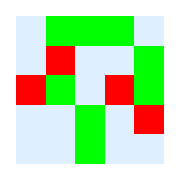

```mathematica
GrilleInitial[n_,pourcentmalade_,pourcentVaccin_] := Module[{tab, etat, proba},
  proba = {pourcentmalade, pourcentVaccin, 1-pourcentmalade-pourcentVaccin};
  etat = {Individu[1,0],Individu[4,0],Individu[0,0]};
  tab = Table[RandomChoice[proba -> etat], {n}, {n}];
  tab
]

n = 5;
result = GrilleInitial[n,0.1,0.4];
ArrayPlot[result /. {{0, _} -> Green, {1, _} -> Red, {4, _} -> LightBlue},ImageSize->Small]
```

Nous devons à présent déterminer la condition d’infection d’une cellule qui dépend de ces voisines. Une première approche très simpliste mais permettant d’obtenir un première première version fonctionnel du modèle est de considéré un voisinage direct (les 8 cellules autour d’un individu comme pour le Jeu de la vie) et de multiplier le nombre de cellule voisine malade par une probabilités d’infection (en faisant attention que le résultat ne soit pas supérieur à 1). Cette méthode doit être in fine remplacé par une loi binomiale

```mathematica
(*calcul de proba*)
newprobaTransmission3x3[probaTransmission_,grille3x3_]:= Module[{nbDeMalade,prob},
	nbDeMalade=Count[Flatten[grille3x3,1],{1, _}]; (*Compte le nombre de cellule malade*)
	prob=nbDeMalade*probaTransmission;
	If[prob>1,1,prob]
]
```

On peut maintenant écrire la fonction pour faire évoluer la liste, on utilise ici Partition car la fonction pour définir un cercle de voisins ne marche pas encore. La structure du programme reste similaire à celui fait pour le Jeu de la vie on a juste quelque conditions en plus.  Pour déterminer quand une cellule tombe malade ou meurt, on va générer un nombre aléatoire entre 0 et 1 que l’on va comparer à la probabilité de mort ou d’infection, si on est inférieur à ce nombre alors on modifie l’état de la cellule. Par exemple si la probabilité de mort est 0.4 alors pour que la cellule meurt il faut que le nombre générer par RandomReal soit inférieur à 0.4 ce qui à 40% de chance de ce produire. La seule chose qui change avec le programme du Jeu de la vie c’est les effets de bords, comme ou se considère sur un tore on va utiliser la fonction ArrayPad avec les paramètres “periodic” et le offset. Le paramètre “periodic” permet de “connecter” chaque bord en ajoutant respectivement en début et fin de liste la dernière et la première liste et de même en début et fin de chaque sous liste, le offset sous la forme d’un tableau également {{_,_},{_,_}} permet de préciser pour chacun des bords combien de ligne ou colonne veut-on rajouter du bord opposé, ici c’est 1 car on utilise Partition seulement sur les voisins direct.

```mathematica
evolutionEpidemie[grille_, probinfection_, probmort_, tempsGuerison_,tempsimm_] := Module[{newGrille, voisins},
  newGrille = ArrayPad[grille, {{1, 1}, {1, 1}}, "Periodic"];
  voisins = Partition[newGrille, {3, 3}, {1,1}];
  Do[
    If[grille[[i, j]][[1]] == 0 && RandomReal[] < newprobaTransmission3x3[probinfection,voisins[[i,j]]],
       newGrille[[i+1, j+1]] = Individu[1,1]
       ];
    If[grille[[i, j]][[1]] == 1,
       If[RandomReal[] < probmort,
          newGrille[[i+1, j+1]] = Individu[2,0], (*si le cellule meurt on change son état en 2*)
          newGrille[[i+1, j+1]] = Individu[1, newGrille[[i+1, j+1]][[2]] + 1] (*sinon on incrémente la vaiable nbdetourmalade de 1*)
          ]
       ];
    If[grille[[i, j]][[1]]==1 && grille[[i, j]][[2]]>=tempsGuerison,(*si la cellule est malade depuis suffisament de tour*)
       newGrille[[i+1,j+1]] = Individu[3,0]
       ];
     If[grille[[i, j]][[1]]==3,
       If[grille[[i, j]][[2]]>=tempsimm,(*si la cellule est immunisé depuis suffisament de tour elle peut retomber malade*)
         newGrille[[i+1,j+1]] = Individu[0,0],
         newGrille[[i+1, j+1]] = Individu[3, newGrille[[i+1, j+1]][[2]] + 1]
         ]
       ],
    {j, Length[grille[[1]]]}, {i, Length[grille]}];
  Take[newGrille,{2,Length[grille]+1},{2,Length[grille[[1]]]+1}]
  ]
```

On peut maintenant faire une fonction qui va simuler l’évolution de l’épidémie n fois grâce à Nest et NestList. L’évolution est plutôt longue donc pour ne pas afficher 40 images à la suite, nous utiliserons la fonction Nest tout les 10t pour pouvoir voir comment se comporte l’épidémie asymptotiquement. Il existe sur Mathematica une fonction ListAnimate qui permet de faire un gif de l’épidémie.

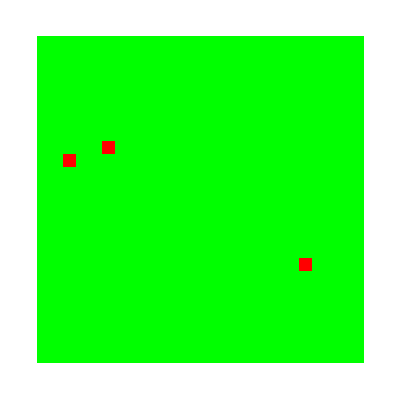
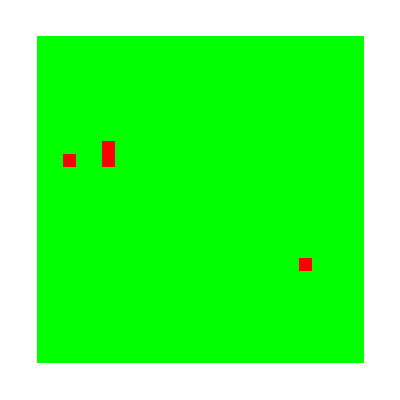
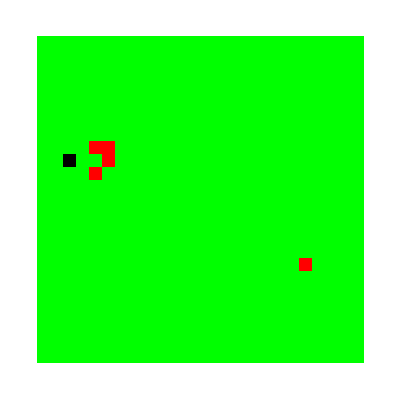
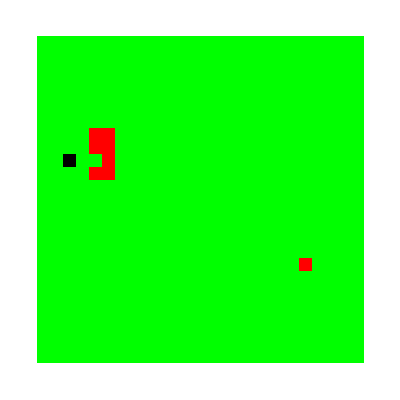
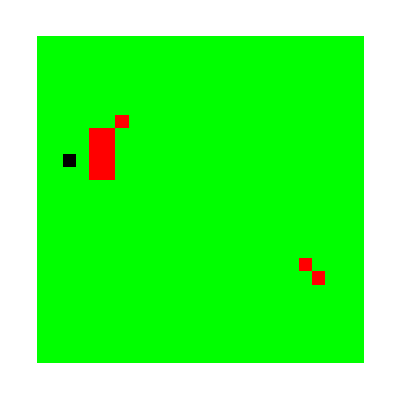
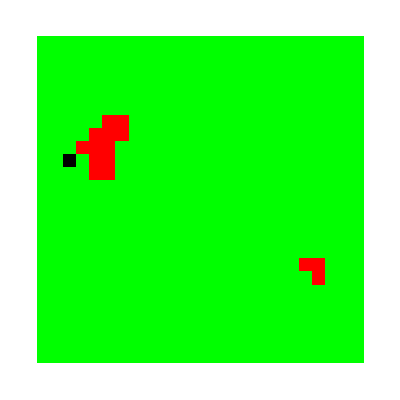
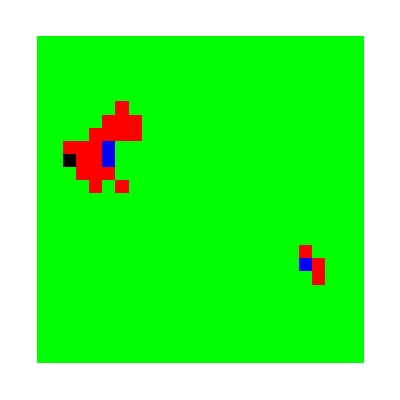
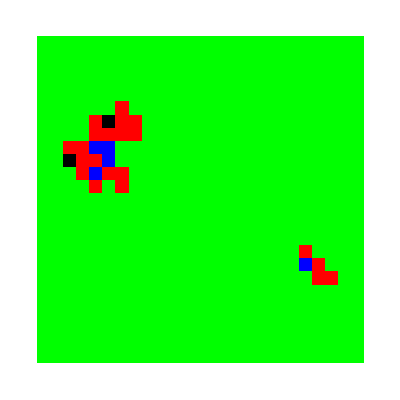

```mathematica
PropagEpidemie[init_,n_,probInfection_,probmort_,tgueri_,timm_]:= NestList[evolutionEpidemie[#, probInfection, probmort, tgueri,timm] &, init, n]
PropagEpidemieInstantN[init_,n_,probInfection_,probmort_,tgueri_,timm_]:= Nest[evolutionEpidemie[#, probInfection, probmort, tgueri,timm] &, init, n]

init = GrilleInitial[25,0.01,0];
evol = PropagEpidemie[init,10,probInfection,probMort,gueri,imm];
ArrayPlot[# /. {{0, _} -> Green, {1, _} -> Red, {2, _}-> Black, {3, _}->Blue, {4, _}->LightBlue}, ImageSize->Tiny] &/@ evol
toutLes10t = {PropagEpidemieInstantN[init,20,probInfection,probMort,gueri,imm],PropagEpidemieInstantN[init,30,probInfection,probMort,gueri,imm],PropagEpidemieInstantN[init,40,probInfection,probMort,gueri,imm],
PropagEpidemieInstantN[init,50,probInfection,probMort,gueri,imm],PropagEpidemieInstantN[init,60,probInfection,probMort,gueri,imm],PropagEpidemieInstantN[init,70,probInfection,probMort,gueri,imm],
PropagEpidemieInstantN[init,80,probInfection,probMort,gueri,imm],PropagEpidemieInstantN[init,90,probInfection,probMort,gueri,imm]};
(*ListAnimate[ArrayPlot[ # /. {{0, _} -> Green, {1, _} -> Red, {2, _}-> Black, {3, _}->Blue, {4, _}->LightBlue}]  &/@ evol]*)
ArrayPlot[PropagEpidemieInstantN[init,20,probInfection,probMort,gueri,imm] /. {{0, _} -> Green, {1, _} -> Red, {2, _}-> Black, {3, _}->Blue, {4, _}->LightBlue}, ImageSize->Tiny] &/@ toutLes10t
```

On simule tout d’abord une épidémie avec des paramètres initiaux choisis un peu aléatoirement mais qui semble cohérent (maladie au moins 10 fois plus contagieuse que mortel et des durées on l’on est malade et immunisé ni trop long ni trop court).
La première ligne montre l’évolution du début de l’épidémie sur les 10 premières itérations et la seconde ligne montre l’évolution de l’épidémie toute les 10 itérations de la 20ème à la 90ème. Avec ces paramètres initiaux de propagation de mort et de guérison on observe après une période de croissance une certaine stabilité de l’épidémie, après une croissance de l’épidémie chaque itération il y a peu près autant  de cellules qui tombent malade que de cellules qui guérissent, sans aucune prise en charge de la maladie par des vaccins ou des confinements la maladie va continuer à exister en tuant petit à petit chaque individu. On testant d’autre paramètres de départ, on se rend compte que l’on obtient cette stabilité assez facilement tant que la maladie se propage plus vite qu’elle ne tue et que les durées pendant lesquels les cellules sont malades ou immunisées ne sont pas trop courte ou longue (on doit les paramètres imm et gueri du départ compris à peu près entre 3 et 20), si le temps immunisé après la maladie est très court et que celle-ci est relativement contagieuse alors l’épidémie sera stable mais tout le monde sera presque tout le temps contaminé et l’épidémie tuera petit à petit les individus. Il apparaît donc dans notre modèle un phénomène assez remarquable de stabilité et “d’auto-régulation”. Cependant nous pouvons également nous intéresser sous quels conditions une épidémies peu disparaître, par exemple avec une maladie peu contagieuse mais très mortelle on a :

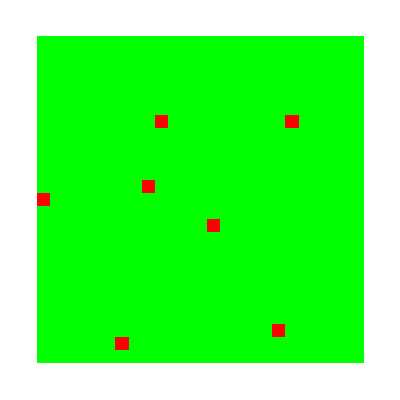
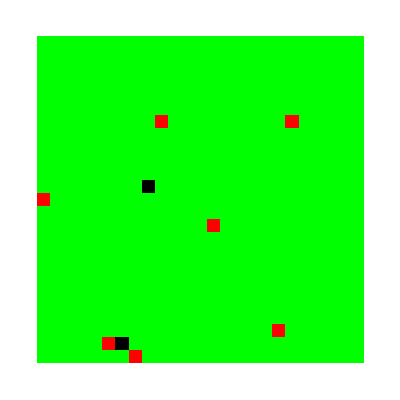
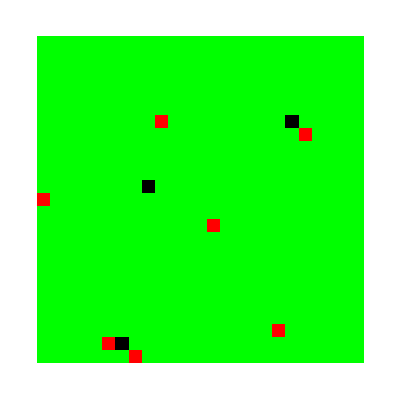
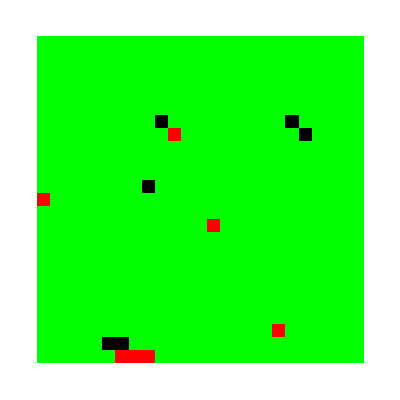
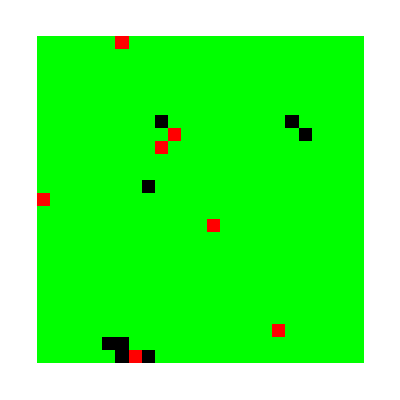
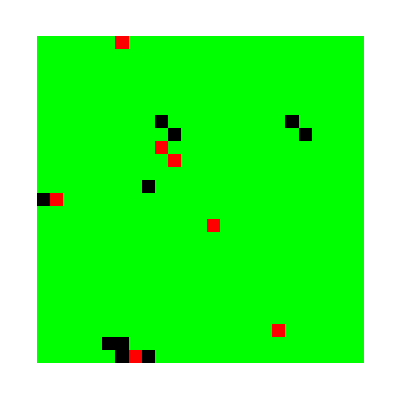
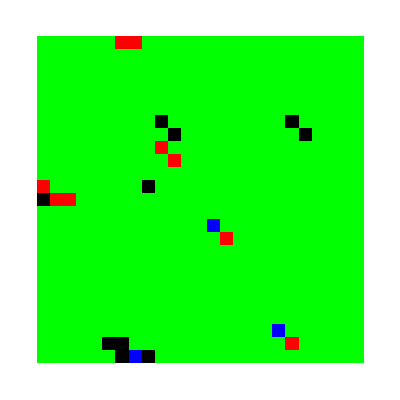
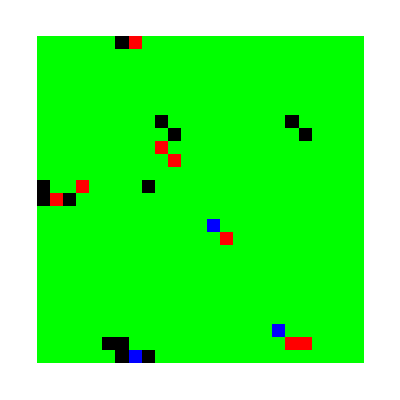

```mathematica
probInfection1 = 0.05;
probMort1 = 0.3;
gueri1=5;
imm1=5;
PropagEpidemie1[init_,n_]:= NestList[evolutionEpidemie[#, probInfection1, probMort1, gueri1,imm1] &, init, n];

init1 = GrilleInitial[25,0.02,0];
evol1 = PropagEpidemie1[init1,25];
(*ListAnimate[ArrayPlot[ # /. {{0, _} -> Green, {1, _} -> Red, {2, _}-> Black, {3, _}->Blue, {4, _}->LightBlue}]  &/@ evol1]*)
ArrayPlot[ # /. {{0, _} -> Green, {1, _} -> Red, {2, _}-> Black, {3, _}->Blue, {4, _}->LightBlue}, ImageSize-> Tiny]  &/@ evol1
```

On observe un résultat que l’on pouvait attendre : la maladie disparaît d’elle même en un faible nombre d’itération (dans notre cas environ 25 itérations à chaque simulation) car les individus meurt plus vite que la maladie se propage.

Effet d’une couverture vaccinale sur la propagation d’une maladie :
On va maintenant introduire des personnes vaccinés, elles sont immunisés indéfiniment à la maladie et donc ne la propage pas. On va observer les effets de couverture vaccinale quand au moins 85% d’une population est vacciné.

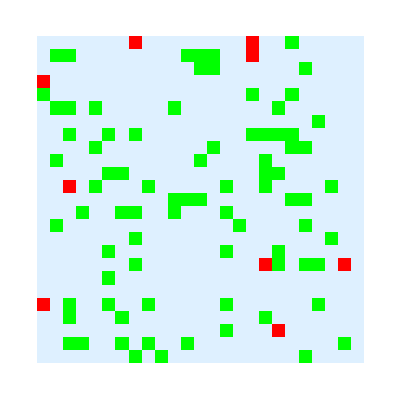
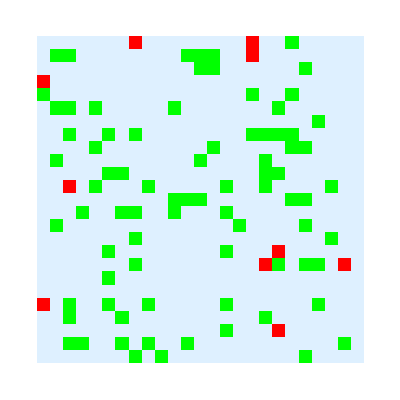
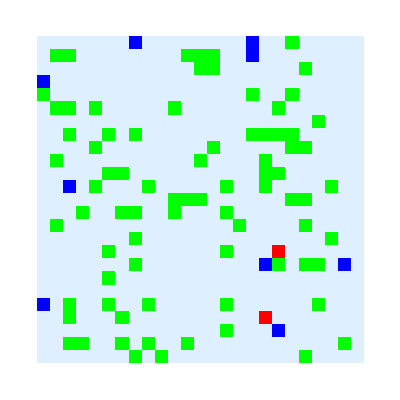
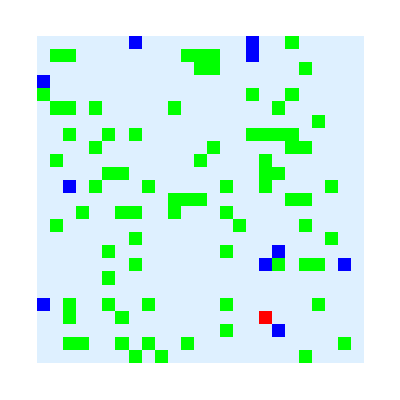
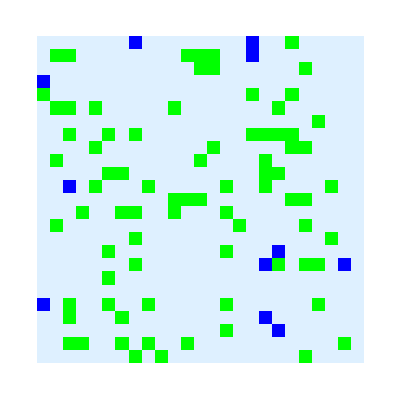
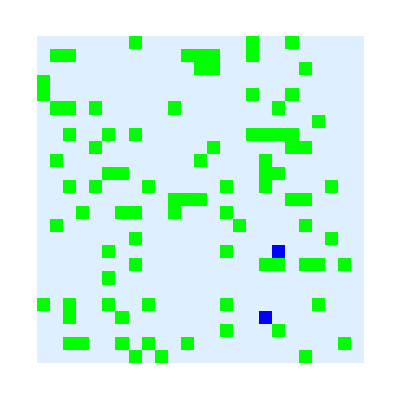
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
initCouvVacc = GrilleInitial[25,0.01,0.85]; (*85% de personne vacciné 14% de non vacciné et 1% de malades*)
evolCouvVacc = PropagEpidemie[initCouvVacc,12,probInfection,probMort,gueri,imm];
(*ListAnimate[ArrayPlot[ # /. {{0, _} -> Green, {1, _} -> Red, {2, _}-> Black, {3, _}->Blue, {4, _}->LightBlue}]  &/@ evolCouvVacc]*)
ArrayPlot[ # /. {{0, _} -> Green, {1, _} -> Red, {2, _}-> Black, {3, _}->Blue, {4, _}->LightBlue}, ImageSize-> Tiny]  &/@ evolCouvVacc
```

On observe que les foyers d’épidémie sont vites limités car bloqué par des personnes vaccinées et la maladie disparais peu à peu. Pour aller plus loin nous pourrons essayer de comparer la limite de couverture vaccinale nécessaire mais nous souhaitons le faire une fois que nous aurons obtenu des fonction de transmission et de voisinage plus poussé.

Pour modéliser une transmission plus poussé de la maladie, on peut modifier le mode d’interaction des cellules avec leurs voisins.
Modifions la propagation de proche en proche par l’interaction des cellules à distances. On pourrait voir cela comme l’interaction sociale des cellules entre elles, en prenant un cercle d’interaction des  cellules. 
Dans un premier temps prenons un rayon d’interaction constant des cellules, ainsi une cellules peut interagir avec tout ses voisins compris dans un disque de rayon R que l’on peut modifier.
Dans ce cas, on peut considérer que les cellules au bord sont en contact avec les cellules de l’autre bord car nous ne sommes plus sur des contacts physique mais sociaux.
Pour cela on peut tracer un disque remplit de 1 dans un tableau remplit de zéros.Puis on fusionne ce tableau que l’on peut nommer tableau d’interaction binaire avec des sous tableau de taille 3 fois le rayon d’interaction, cela à été paramétré par expérience pour éviter des tableaux d’interaction remplit de 1 et pour limiter le nombre de cellules traité. 
Les sous-tableau ainsi obtenue sont remplit d’individu dont les états sont soit leur état de base, soit -1 c’est à dire hors du cercle d’interaction.

```mathematica
disqueMatrice[taille_Integer, rayon_Integer] := Module[{tableau, centre, disque},
  tableau = ConstantArray[0, {taille, taille}];
  centre = Ceiling[taille/2];
  disque = DiskMatrix[rayon, taille];
  disque = ArrayPad[
    disque, {{0, taille - Length[disque]}, {0, 
      taille - Length[disque]}}];
  tableau + disque
]

testBernoulli[n_,p_]:=RandomVariate[BernoulliDistribution[p],n]

fusionMatrice[tableauPartionner_,probaInfection_,matriceCirculaire_]:=Module[{resultatFusion,tabPart,tabPlat,matriceplat,positif,fini,k},
tabPart = tableauPartionner;
resultatFusion= 0;
matriceplat = Flatten[matriceCirculaire];
tabPlat = Flatten[tabPart,1];
positif = False;
k=1;
While[!positif && k < Length[tabPlat],
			If[matriceplat[[k]]== 1,(*Si la cellule est dans le rayon d'action*)
				If[ tabPlat[[k]][[1]]==1,resultatFusion= testBernoulli[1,probaInfection][[1]](*Si la cellule est malade*);
					If[ resultatFusion== 1 , positif = True](*Condition d'arret du while pour gagner du temps de calcul*)
				];
			];
			k++;
];
resultatFusion(*retourne 1 ou 0 en fonction des états des autres cellules *)
]
```

Une fois le tableau d' interaction obtenues pour chaque cellules du tableau initiale, on effectue un test de Bernoulli par cellules malade dans son cercle d' interaction .

```mathematica
evolutionEpidemie2[grille_, probinfection_, probmort_, tempsGuerison_,tempsimm_,rayon_] := Module[{newGrille, voisins,matriceCirculaire},
  newGrille = ArrayPad[grille, {{rayon, rayon}, {rayon, rayon}}, "Periodic"];
  voisins = Partition[newGrille,{2*rayon+1,2*rayon+1}, {1,1}];
  matriceCirculaire =disqueMatrice[2*rayon + 1, rayon];
   Do[
    If[grille[[i, j]][[1]] == 0 && fusionMatrice[voisins[[i,j]],probinfection,matriceCirculaire]==1,
       newGrille[[i+1, j+1]] = Individu[1,1]
       ];
    If[grille[[i, j]][[1]] == 1,
       If[RandomReal[] < probmort,
          newGrille[[i+1, j+1]] = Individu[2,0], (*si le cellule meurt on change son état en 2*)
          newGrille[[i+1, j+1]] = Individu[1, newGrille[[i+1, j+1]][[2]] + 1] (*sinon on incrémente la vaiable nbdetourmalade de 1*)
          ]
       ];
    If[grille[[i, j]][[1]]==1 && grille[[i, j]][[2]]>=tempsGuerison,(*si la cellule est malade depuis suffisament de tour*)
       newGrille[[i+1,j+1]] = Individu[3,0]
       ];
     If[grille[[i, j]][[1]]==3,
       If[grille[[i, j]][[2]]>=tempsimm,(*si la cellule est immunisé depuis suffisament de tour elle peut retomber malade*)
         newGrille[[i+1,j+1]] = Individu[0,0],
         newGrille[[i+1, j+1]] = Individu[3, newGrille[[i+1, j+1]][[2]] + 1]
         ]
       ],
    {j, Length[grille[[1]]]}, {i, Length[grille]}];
  Take[newGrille,{2,Length[grille]+1},{2,Length[grille[[1]]]+1}]
  ]
```

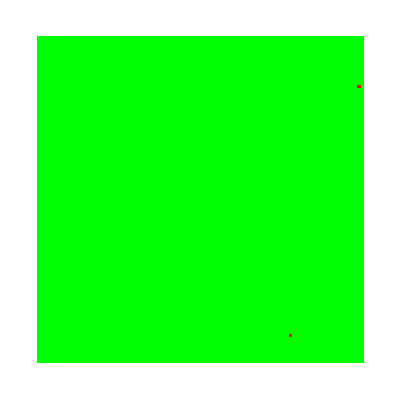
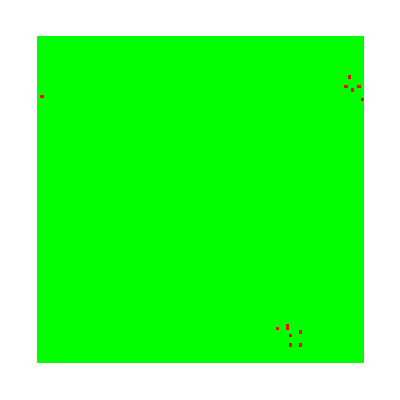
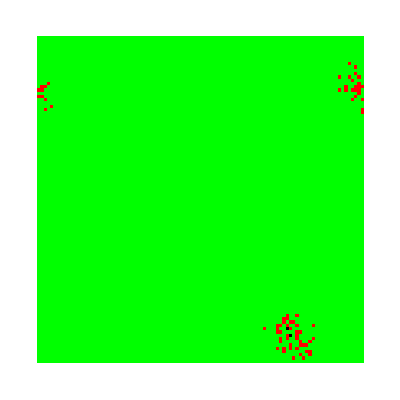
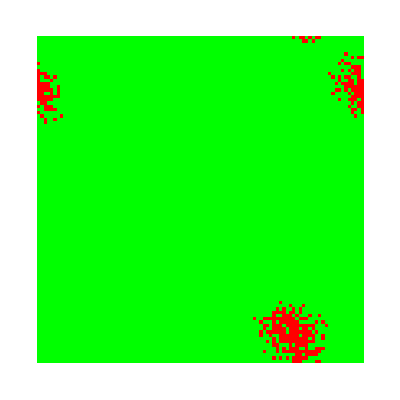
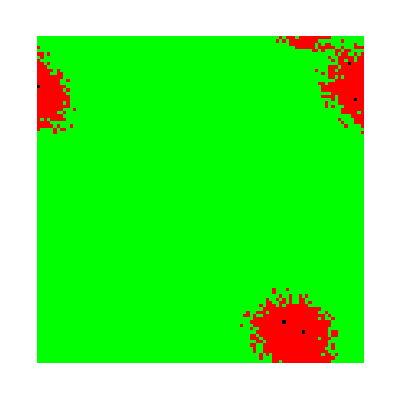
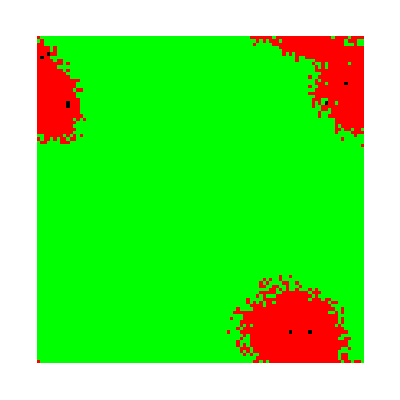
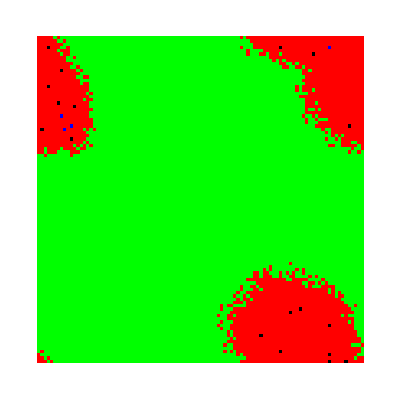
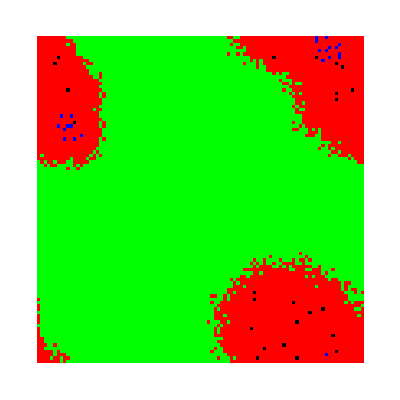
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PropaEpidemie2[init_,n_,probInfection_,probmort_,tgueri_,timm_,rayon_]:= NestList[evolutionEpidemie2[#,probInfection, probmort, tgueri,timm,rayon] &, init, n]
SeedRandom[567];
init2 = GrilleInitial[100,0.0002,0];
evol2 = PropaEpidemie2[init2,50,probInfection,probMort,gueri,imm,4];
ArrayPlot[# /. {{0, _} -> Green, {1, _} -> Red, {2, _}-> Black, {3, _}->Blue, {4, _}->LightBlue}, ImageSize->Tiny] &/@ evol2
```

On remarque lors de la première phase de propagation des sortes de vague de transmission jusqu’à arriver à un mélange homogène (les phases sont mélangés en tout point et il n’y a pas d’endroit avec une phase prédominante)

### Limite de la simulation et perspectives d’amélioration

Notre simulation permet de mettre en évidence des éléments intéressants cependant nous ne pouvons rien affirmer quand à la véracité de nos résultats car il faudrait comparer à des vraies épidémies documenté afin d’affiner les paramètres d’évolution de la simulation. 
Des points restent tout de même à améliorer si nous souhaitons rendre notre simulation plus réaliste à commencé par le déplacement de population. En effet dans les hypothèses de notre simulation les individus sont immobiles, cependant si on veut créer un déplacement de foule il faudrait revoir entièrement le code et les automates cellulaires ne sont pas forcément la meilleure façon de simuler les déplacements.

## III. Application à la propagation de feux de forêt

### Introduction et définition de la grille initiale

Dans cette partie, chaque cellule va donc correspondre à une parcelle de terre d’un territoire. De la même manière que pour une maladie, l’état d’une parcelle peut être défini de plusieurs manières : 
-	(1) parcelle intacte : pas encore atteinte par le feu, correspond à une cellule saine ;
-	(2) parcelle en feu : elle est en train de brûler et peut pendant ce moment propager l’incendie ;
-	(3) parcelle calcinée : elle n’est plus en feu, elle correspondrait à une cellule morte, elle ne peut donc ni reprendre feu, ni propager l’incendie.
La différence la plus importante avec notre modélisation des épidémies est qu’ici nous ne pouvons pas négliger la « nature » des cellules : en effet, il faut donc définir les différents types de parcelles qui peuvent exister : 
-	(1) de l’herbe : brûle rapidement 
-	(2) des rochers : ne brûlent pas et ne transmettent pas l’incendie
-	(3) des arbres : s’enflamment plus difficilement que l’herbe, mais brûlent plus longtemps, donc ils peuvent propager l’incendie autour d’eux plus longtemps
-	(4) des parcelles d’eau : elles ont un rôle similaire aux rochers, elles correspondraient à des flaques, des lacs, des ruisseaux, …
Une autre différence avec la modélisation d’épidémie est que nous ne devons avoir pour départ de feu qu’une seule parcelle, que l’on ne définira donc qu’après que la forêt soit définie par les 4 premières natures de parcelles aléatoirement. Nous créerons donc un cinquième état correspondant au foyer (5), qui sera donc une parcelle brûlant pendant un temps intermédiaire entre celui de l’herbe et celui de l’arbre, afin d’être sûr que l’incendie démarre.

```mathematica
Parcelle[etat_,nature_,tempsContact_,tempsEnFeu_]:={etat,nature,tempsContact,tempsEnFeu};
SeedRandom[123];
GrilleInitial[n_Integer, pourcentageRocher_, pourcentageArbre_,pourcentageEau_] := Module[{array, nature},
  array = Table[
    Parcelle[0,
      nature = RandomReal[];
      If[nature < pourcentageRocher, 1,
       If[nature < pourcentageRocher + pourcentageArbre, 2,
        If[nature < pourcentageRocher + pourcentageArbre + pourcentageEau, 3, 0]]],0,0], 
    {n}, {n}];
  {foyerX, foyerY} = {Quotient[n,2],Quotient[n,2]}; (* Choix aléatoire des coordonnées du foyer *)
  array[[foyerX, foyerY]] = Parcelle[1, 4, 0, 1]; (* Modification de la nature de la case choisie en "Foyer" *)
  array
]


m = 50;
result = GrilleInitial[m,0.1,0.4,0.05];
ArrayPlot[result /. {{ _, 0, _, _} -> Green, { _, 1, _, _} -> Gray, { _, 2, _, _} -> Brown, { _, 3, _, _} -> Blue, { _, 4, _, _} -> Red},ImageSize->Small]
```

-Graphics-

### Importation d’image

```mathematica
(* Charger l'image *)
imagePath = "Z:\\Bureau\\mu1\\S_Jaune\\math\\projet\\projet mathematica\\foret2.jpg";
image = Import[imagePath];

(* Réduire la taille de l'image *)
imageReduite = ImageResize[image, Scaled[0.05]]; (* Réduit la taille de l'image de moitié *)

(* Analyser les couleurs *)
imageData = ImageData[imageReduite];

(* Déterminer la nature des parcelles en fonction des couleurs *)
natureDeParcelle[couleur_List] := Module[{rouge, vert, bleu},
  {rouge, vert, bleu} = couleur;
  (* Définir ici les seuils de couleur et les natures correspondantes *)
  Which[
   rouge < 0.1 && vert < 0.8 && vert > 0.5 && bleu < 0.1, 0, (* Herbe *)
   rouge < 0.1 && vert < 0.1 && bleu < 0.1, 1, (* Rocher *)
   rouge < 0.4 && vert > 0.3 && bleu < 0.2, 2, (* Arbre *)
   rouge > 0.3 && vert > 0.4 && bleu > 0.45, 3, (* Eau *)
   True, 0 (* Par défaut, considérer comme de l'herbe *)
   ]
];

(* Générer la grille *)
grilleAPartirImage = Table[
   Parcelle[0, natureDeParcelle[imageData[[i, j]]], 0, 0],
   {i, Length[imageData]}, {j, Length[imageData[[1]]]}
];

{m, n, w} = Dimensions[grilleAPartirImage];
{foyerX, foyerY} = {Quotient[m,2]-10,Quotient[n,2]};
grilleAPartirImage[[foyerX, foyerY]] = Parcelle[1, 4, 0, 1];


(* Afficher la grille *)
ArrayPlot[grilleAPartirImage /. {
   {_, 0, _, _} -> Green, (* Herbe *)
   {_, 1, _, _} -> Gray,  (* Rocher *)
   {_, 2, _, _} -> Brown, (* Arbre *)
   {_, 3, _, _} -> Blue,  (* Eau *)
   {_, 4, _, _} -> Red
   },
 ImageSize -> Small
]
```

-Graphics-

### Évolution de l’incendie

Il nous faut créer une fonction qui fera évoluer la grille à chaque tour. Le principe est le même que pour les épidémies : on parcourt chaque cellule, et on change son état en fonction des cellules immédiatement autour (8 cellules). 
Ici, nous avons introduit un compteur pour les parcelles d’herbe et d’arbres qui s’incrémentera chaque tour suivant la présence ou non de cellules en feu autour. Une fois que ce compteur dépasse une certaine limite, la cellule prend feu.
Pour les cellules en feu, le raisonnement est similaire. Chaque tour, un compteur s’incrémente pour relever le temps que la cellule a passé à brûler. Au bout d’un certain nombre de tour, la cellule passe à l’état calciné. On peut noter qu’il ne faut pas oublier, en plus des cellules d’herbe et d’arbre, de gérer l’évolution de la cellule correspondra au foyer. En effet, bien que sa nature initiale soit différente, elle aussi finira par passer à l’état calciné.

```mathematica
evolutionFeuDeForet1[grille_, tempsDePropagationHerbe_, tempsDePropagationArbre_, tempsBrulureHerbe_, tempsBrulureArbre_, tempsBrulureFoyer_] := Module[{newGrille, voisins, nbDeParcelleEnFeu},
  newGrille = ArrayPad[grille, {{1, 1}, {1, 1}}, Parcelle[0,5,0,0]];
  voisins = Partition[newGrille, {3, 3}, {1,1}];
  Do[
    nbDeParcelleEnFeu = Count[Flatten[voisins[[i,j]],1],{1, _, _, _}];
    If[nbDeParcelleEnFeu > 0, newGrille[[i+1,j+1]][[3]] = newGrille[[i+1,j+1]][[3]] + nbDeParcelleEnFeu];
    If[grille[[i, j]][[1]] == 0 && grille[[i,j]][[2]] == 0 && newGrille[[i+1,j+1]][[3]] > tempsDePropagationHerbe, (*Si la parcelle d'herbe a été en contact avec le feu trop longtemps, elle prend feu*)
       newGrille[[i+1, j+1]][[1]] = 1
       ];
    If[grille[[i, j]][[1]] == 0 && grille[[i,j]][[2]] == 2 && newGrille[[i+1,j+1]][[3]] > tempsDePropagationArbre, (*Si la parcelle arbre a été en contact avec le feu trop longtemps, elle prend feu*)
       newGrille[[i+1, j+1]][[1]] = 1
       ];
    If[grille[[i, j]][[1]] == 1 && grille[[i, j]][[2]] == 0,
       If[grille[[i, j]][[4]] > tempsBrulureHerbe, 
          newGrille[[i+1, j+1]][[1]] = 2, (*si la parcelle d'herbe a brulé assez longtemps, elle est morte (cramée)*)
          newGrille[[i+1, j+1]][[4]] = newGrille[[i+1, j+1]][[4]]+1 (*sinon on incrémente la variable tempsEnFeu de 1*)
          ]
       ];
    If[grille[[i, j]][[1]] == 1 && grille[[i, j]][[2]] == 2,
       If[grille[[i, j]][[4]] > tempsBrulureArbre, 
          newGrille[[i+1, j+1]][[1]] = 2, (*si la parcelle arbre a brulé assez longtemps, elle est morte (cramée)*)
          newGrille[[i+1, j+1]][[4]] = newGrille[[i+1, j+1]][[4]]+1 (*sinon on incrémente la variable tempsEnFeu de 1*)
          ]
       ];
    If[grille[[i, j]][[1]] == 1 && grille[[i, j]][[2]] == 4,
       If[grille[[i, j]][[4]] > tempsBrulureFoyer,
          newGrille[[i+1, j+1]] = Parcelle[2,grille[[i, j]][[2]],grille[[i, j]][[3]],grille[[i, j]][[4]]], (*si le foyer a brulé assez longtemps, elle est morte (cramée)*)
          newGrille[[i+1, j+1]] = Parcelle[1,grille[[i, j]][[2]],grille[[i, j]][[3]],grille[[i, j]][[4]]+1] (*sinon on incrémente la variable tempsEnFeu de 1*)
          ]
       ];
    ,
    {j, Length[grille[[1]]]}, {i, Length[grille]}];
  Take[newGrille,{2,Length[grille]+1},{2,Length[grille[[1]]]+1}]
  ]
```

```mathematica
SeedRandom[123];
grilleDeDepart = grilleAPartirImage;
evolution1 = NestList[evolutionFeuDeForet1[#, 1, 2, 3, 5, 4] &, grilleDeDepart, 30];

arrayPlots = ArrayPlot[ # /. {{0, 0, _, _} -> Green, (* Herbe intacte *)
    {0, 1, _, _} -> Gray, (* Rocher *)
    {0, 2, _, _} -> Brown, (* Arbre intact *)
    {0, 3, _, _} -> Blue,  (* Eau *)
    {0, 4, _, _} -> Red,   (* Foyer *)

    {1, _, _, _} -> Red,   (* Parcelle en feu *)
    {2, _, _, _} -> Black}, ImageSize->Tiny]  &/@ evolution1 (* Parcelle éteinte *)
(*ListAnimate[arrayPlots]*)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

La première ligne montre l’évolution lors des 10 premières itérations et la deuxième montre l’évolution de l’incendie de 10 en 10 de la 20ème à la 60ème itération.
La propagation de l’incendie se fait correctement, on observe effectivement une propagation des cellules en feu dans toutes les directions, sans que les parcelles d’eau et de roche soient affectées.

### Influence du vent

Jusqu’ici, le feu se propage dans toutes les directions à partir du foyer, ce qui ne correspond pas tellement à la réalité puisque bien souvent le vent donne une direction principale de propagation aux feux de forêt. Le but de cette amélioration est donc de proposer une modélisation du vent.
L’idée pour prendre en compte le vent est de pondérer l’influence de chacune des parcelles voisines en fonction de leur position autour de la cellule centrale : imaginons que le vent est orienté en direction du nord-ouest, alors les cellules situées au sud-est de la cellule centrale aurons plus d’influence pour mettre la cellule au centre en feu que les cellules au nord-ouest : 
-Graphics-
On compte alors le nombre de cellules en feu autour de la cellule centrale comme avant, mais cette fois, au lieu d’incrémenter le compteur de 1, il augmentera du facteur de pondération correspondra. Ainsi les cellules se présentant dans la direction du vent s’enflammeront plus vite que les cellules à l’opposé, qui n’auront tout simplement pas le temps de prendre feu.

On stocke dans un premier lieu les matrices représentant les facteur de pondération selon l’orientation : “se” pour Sud-Est, “no” pour Nord-Ouest, etc.

```mathematica
se = {{1,0.6,0.4},{0.6,0,0.2},{0.4,0.2,0}};
s = {{0.6,1,0.6},{0.2,0,0.2},{0,0,0}};
so = {{0.4,0.6,1},{0.2,0,0.6},{0,0.2,0.4}};
e = {{0.6,0.2,0},{1,0,0},{0.6,0.2,0}};
o = {{0,0.2,0.6},{0,0,1},{0,0.2,0.6}};
ne = {{0.4,0.2,0},{0.6,0,0.2},{1,0.6,0.4}};
n = {{0,0,0},{0.2,0,0.2},{0.6,1,0.6}};
no = {{0,0.2,0.4},{0.2,0,0.6},{0.4,0.6,1}};
```

La différence dans la fonction d’évolution se fait au niveau du compte du nombre de parcelles en feu : ici, on extrait une liste de 1 et de 0 correspondant à l’état “en feu” d’une cellule ou non. Ensuite, on effectue simplement un produit scalaire entre cette liste, et la liste obtenue après diminution d’une dimension de la liste correspondant aux facteurs de vent. Ce compte est ensuite réutilisé pour incrémenter le temps de contact avec une cellule en feu.

```mathematica
evolutionFeuDeForet2[grille_, tempsDePropagationHerbe_, tempsDePropagationArbre_, tempsBrulureHerbe_, tempsBrulureArbre_, tempsBrulureFoyer_, directionVent_] := Module[{newGrille, voisins, nbDeParcelleEnFeu},
  {rows, cols, what} = Dimensions[grille];
  newGrille = ConstantArray[{0, 5, 0, 0}, {rows + 2, cols + 2}];
  Do[
     newGrille[[i + 1, j + 1]] = grille[[i, j]],
     {i,2, rows}, {j,2, cols}
   ];
  voisins = Partition[newGrille, {3, 3}, {1,1}];
  Do[
     listeVoisinsEnFeu = {};
     Do[
        If[voisins[[i,j]][[k]][[l]][[1]] == 1, AppendTo[listeVoisinsEnFeu,1], AppendTo[listeVoisinsEnFeu,0]]
       , {k, Length[voisins[[i,j]]]},{l,Length[voisins[[i,j]][[1]]]}];
    nbDeParcelleEnFeu = listeVoisinsEnFeu.Flatten[directionVent,1];
    If[nbDeParcelleEnFeu > 0, newGrille[[i+1,j+1]][[3]] = newGrille[[i+1,j+1]][[3]] + nbDeParcelleEnFeu];
    If[grille[[i, j]][[1]] == 0 && grille[[i,j]][[2]] == 0 && newGrille[[i+1,j+1]][[3]] > tempsDePropagationHerbe, (*Si la parcelle d'herbe a été en contact avec le feu trop longtemps, elle prend feu*)
       newGrille[[i+1, j+1]] = Parcelle[1,4,grille[[i, j]][[3]],grille[[i, j]][[4]]+1]
       ];
    If[grille[[i, j]][[1]] == 0 && grille[[i,j]][[2]] == 2 && newGrille[[i+1,j+1]][[3]] > tempsDePropagationArbre, (*Si la parcelle arbre a été en contact avec le feu trop longtemps, elle prend feu*)
       newGrille[[i+1, j+1]] = Parcelle[1,4,grille[[i, j]][[3]],grille[[i, j]][[4]]+1]
       ];
    If[grille[[i, j]][[1]] == 1 && grille[[i, j]][[2]] == 0,
       If[grille[[i, j]][[4]] > tempsBrulureHerbe,
          newGrille[[i+1, j+1]] = Parcelle[2,grille[[i, j]][[2]],grille[[i, j]][[3]],grille[[i, j]][[4]]], (*si la parcelle d'herbe a brulé assez longtemps, elle est morte (cramée)*)
          newGrille[[i+1, j+1]] = Parcelle[1,grille[[i, j]][[2]],grille[[i, j]][[3]],grille[[i, j]][[4]]+1] (*sinon on incrémente la variable tempsEnFeu de 1*)
          ], Null
       ];
    If[grille[[i, j]][[1]] == 1 && grille[[i, j]][[2]] == 2,
       If[grille[[i, j]][[4]] > tempsBrulureArbre,
          newGrille[[i+1, j+1]] = Parcelle[2,grille[[i, j]][[2]],grille[[i, j]][[3]],grille[[i, j]][[4]]], (*si la parcelle arbre a brulé assez longtemps, elle est morte (cramée)*)
          newGrille[[i+1, j+1]] = Parcelle[1,grille[[i, j]][[2]],grille[[i, j]][[3]],grille[[i, j]][[4]]+1] (*sinon on incrémente la variable tempsEnFeu de 1*)
          ], Null
       ];
    If[grille[[i, j]][[1]] == 1 && grille[[i, j]][[2]] == 4,
       If[grille[[i, j]][[4]] > tempsBrulureFoyer,
          newGrille[[i+1, j+1]] = Parcelle[2,grille[[i, j]][[2]],grille[[i, j]][[3]],grille[[i, j]][[4]]], (*si le foyer a brulé assez longtemps, elle est morte (cramée)*)
          newGrille[[i+1, j+1]] = Parcelle[1,grille[[i, j]][[2]],grille[[i, j]][[3]],grille[[i, j]][[4]]+1] (*sinon on incrémente la variable tempsEnFeu de 1*)
          ], Null
       ];
    ,
    {j, Length[grille[[1]]]}, {i, Length[grille]}];
  Take[newGrille,{2,Length[grille]+1},{2,Length[grille[[1]]]+1}]
  ]
```

```mathematica
grilleDeDepart1 = grilleAPartirImage;
evolution1 = NestList[evolutionFeuDeForet2[#, 1, 2, 3, 5, 4,se] &, grilleDeDepart1, 40];

arrayPlots = ArrayPlot[ # /. {{0, 0, _, _} -> Green, (* Herbe intacte *)
    {0, 1, _, _} -> Gray, (* Rocher *)
    {0, 2, _, _} -> Brown, (* Arbre intact *)
    {0, 3, _, _} -> Blue,  (* Eau *)
    {0, 4, _, _} -> Red,   (* Foyer *)
    {0, 5, _, _} -> White,    (*Bord*)

    {1, _, _, _} -> Red,   (* Parcelle en feu *)
    {2, _, _, _} -> Black}, ImageSize->Tiny]  &/@ evolution1 (* Parcelle éteinte *)
(*ListAnimate[arrayPlots]*)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

La propagation est effectivement favorisée dans la direction du vent donnée en argument. Ici par exemple, les parcelles au Nord-Ouest du foyer prennent feu facilement, tandis que les parcelles au sud-est ne semble pas ou presque pas évoluer.

### Discussions et perspectives

Tout comme pour le modèle de simulation d’épidémies ce modèle n’est pas comparable avec des réels feu de forêt car il faudrait procéder à une analyse complète pour déterminer 
Il pourrait être intéressant de modéliser le vent tel qu’il serait si fort que des parcelles non immédiatement voisines pourraient être affectées par le feu aussi. Illustration :
-Graphics-
De cette manière, le feu pourrait se propager encore plus vite et se propager au delà de certains obstacles.

## Conclusion

Ce projet a permis de mettre en avant l’utilité des automates cellulaires pour la simulation de phénomènes physiques, en particulier des propagations. Il reste tout de même quelques points que nous pouvons améliorer à commencer par une modification de la densité de population pour la propagation de maladie. Le fait d’avoir une population non mobile est un choix criticable mais ajouter un déplacement de population nécessiterait une refonte total du code et les automates cellulaires ne sont pas forcément le type de programme le plus adapté pour cela car très lourd en calculs.
Pour la propagation de feu forêt, nous pourrions trouver un moyen de régler les coefficients RGB pour qu’ils correspondent au bon type de parcelle pour n’importe quelle image trouvée sur internet. D’autre part, il peut être intéressant de développer la capacité du vent à se propager, comme expliqué précédemment. Notre modélisation nous permet néanmoins d’étudier le phénomène de propagation pour n’importe quelle direction du vent pour un type de forêt classique.
Le point faible de ce projet est sans doute la complexité algorithmique de nos fonctions et la manipulation de nombreux tableaux de grande taille, on a rencontré de nombreux problèmes avec Mathematica durant ce projet, dès la moindre erreur Mathematica l’applique a tout les éléments d’une liste ce qui fait planté le logiciel en boucle et ce qui nous a fait perdre de nombreuses heures de travail. 
Enfin, il est important de préciser que ce projet n’a pas pour but de simuler de manière précise des épidémies ou des feux de forêt mais simplement de mettre en place des bases de simulation. Il manque à ce projet une grosse partie d’analyse de données (en ce basant sur des vraies épidémies et incendies) pour pouvoir déterminer les coefficients les plus justes (coefficients de propagation, de mortalité, guérison...).

## Bibliographie

Un certain nombre de documentation nous a aider dans ce projet:
- [1] Tables of Cellular Automaton Properties, Stephen Wolfram, 1986 : https://files.wolframcdn.com/pub/www.stephenwolfram.com/pdf/cellular-automata-self-organizing-systems.pdf. Ce document fait la liste de l’ensemble des règles d’automates cellulaires 		existant déjà sur Mathematica.
- [2] Les automates cellulaires : Le Jeu de la vie, Jean Debord, Université de Limoges : https://www.unilim.fr/pages_perso/jean.debord/fbcroco/jeu_de_la_vie.pdf. Résumant le Jeu de la vie et présentant certains motifs récurant.
-  [3] Fourmi de Langton : https://www.unilim.fr/pages_perso/jean.debord/fbcroco/fourmi_de_langton.pdf
- [4] Automates cellulaires et phénomènes d’auto-organisation : le rôle de l’aléa, Irène Marcovici, 2023 : https://epi.asso.fr/revue/articles/a2310c.htm#HPAGE. Présentant le rôle de l’aléatoire dans les automates cellulaire.
- [5] Development of an epidemic spreading simulator using agent-based cellular automata. Case study : COVID-19.  BOUAOUNE Soumia, FILALI :
 http://dspace.centre-univ-mila.dz/jspui/bitstream/123456789/1397/1/Development%20of%20an%20epidemic%20spreading%20simulator%20using%20agent-based%20cellular%20automata..pdf
- [6] Modélisation de feux de forêts par automates cellulaires, Benlatreche Abdelouahab, 2020 : 
http://dspace.univ-msila.dz:8080/xmlui/bitstream/handle/123456789/21348/Benlatreche%20abdelouahab.pdf?sequence=1

## Annexe Utilisation des fonctions de Mathematica pour les automates cellulaires

Il existe déjà dans Mathematica une fonction pour simuler des automates cellulaire : CellularAutomaton[rule, init, t], avec rule les règles régissant l’automate, init le tableau initial et t le nombre d’étapes que l’on veut simuler. Pour afficher le tableau on peut utiliser la fonction Arrayplot.

### Écriture des règles

Les règles à entrer dans CellularAutomaton sont des entiers naturels obtenus par la conversion en base 10 d'octets binaires, et ces octets portent les règles d'évolution. Prenons l'exemple d'un automate à 1 dimension et définissons les règles suivantes d'évolution de la cellule par rapport à ses voisines (la cellule qui évolue est celle du milieu) : 
-Graphics-
Cela donne :
État des voisines	État de la cellule à l'étape suivante
000				0
001				1
010				1
011				1
100				1
101				0
110				0
111				0
On obtient l'octet suivant : 0001110 en base 10 cela donne :

```mathematica
FromDigits["00011110",2]
```

30

On peut aussi afficher de manière graphique les règles de l’automate de cette manière :

```mathematica
RulePlot[CellularAutomaton[30]]
```

-Graphics-

Cette façon de faire permet d’obtenir des règles pour les automates cellulaires à une dimension

Remarque :  pour certains automates cellulaires les plus connus (Jeu de la vie et la règle 30) il n’est pas nécessaire d’entrer les règles d’évolution mais une chaîne de caractères spéciale peut-être utilisée : “Rule30” et “gameOfLife”.

### Exemple d’automate binaire de dimension 1

Voici quelques exemples d’évolution d’automate cellulaire à une dimension. Chaque ligne correspond à une étape d’évolution, en affichant les itérations à la suite on peut donc observer des motifs apparaître.

```mathematica
(*Exemple d'un automate de taille finie*)
```

```mathematica
init = {0,0,0,0,1,0,0,0,0};
ArrayPlot[CellularAutomaton[30,init,25],ImageSize->Small]

(*Exemple d'un automate de taille illimité*)
ArrayPlot[CellularAutomaton[30,{{1},0},50],ImageSize->Small]
```

-Graphics-

-Graphics-

```mathematica
RulePlot[CellularAutomaton[90]]
ArrayPlot[CellularAutomaton[90,{{1},0},31],ImageSize->Small]
```

-Graphics-

-Graphics-

```mathematica
RulePlot[CellularAutomaton[110]]
ArrayPlot[CellularAutomaton[110,{{1},0},25],ImageSize->Small]
```

-Graphics-

-Graphics-

### Automate binaire à 2 dimensions

Il existe également des règles prédéfinies pour les automates cellulaires 2D,  de plus toutes les règles logiques permettant de définir nos propres règles sont recensées dans une documentation Mathematica [1]. Nous n’entrerons pas dans les détails, car nous nous intéressons principalement au Jeu de la vie qui existe déjà sous l’appellation “GameOfLife”.

```mathematica
Clear["Global`*"]
dim = {20,20};
initial=ArrayPad[RandomInteger[1,dim],1];
GenSuivante[grille_]:=Last[CellularAutomaton["GameOfLife",grille,1]];
(*fonction pour faire évoluer l'automate*)
Evolution[grille_,NbDePas_]:=NestList[GenSuivante,grille,NbDePas];
```

```mathematica
(*Visualisation*)
test=Evolution[initial,5];
```

```mathematica
Visualisation[test]
(*Exportation en format gif*)
(*Export["Z:\\Bureau\\mu1\\S_Jaune\\math\\projet/animation.gif",Visualisation[test]]*)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}